```mathematica
SetDirectory[NotebookDirectory[]]
```

/Volumes/BRETT-STUFF

### Step function model

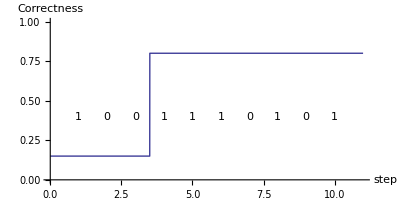

```mathematica
stepPlot=Block[{l=3.5,pg=.15,ps=0.2},Plot[If[x<l,pg,1-ps],{x,0,11},PlotRange->{0,1},Epilog->{Table[Text[If[x<l,If[RandomReal[]>pg,0,1],If[RandomReal[]<ps,0,1]],{x,.4}],{x,1,10}]},AxesLabel->{"step","Correctness"},BaseStyle->{FontSize->12}, AspectRatio->1/2]]
```

```mathematica
Export["step.eps",stepPlot]
```

step.eps

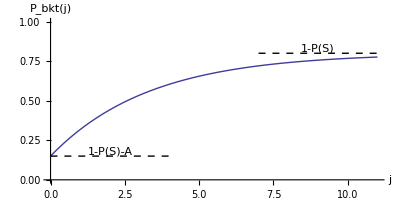

```mathematica
bktPlot=Block[{b=0.3,pg=.15,ps=0.2,nn=11},Plot[1-ps-(1-pg-ps)  Exp[-b x],{x,0,nn},PlotRange->{0,1},AxesLabel->{"j",SequenceForm[Subscript["P","bkt"],"(j)"]},BaseStyle->{FontSize->12}, AspectRatio->1/2,Epilog->{Text["1-P(S)-A",{2,pg},{0,-1}],Text["1-P(S)",{nn-2,1-ps},{0,-1}],Dashed,Line[{{0,pg},{4,pg}}],Line[{{nn-4,1-ps},{nn,1-ps}}]}]]
```

```mathematica
Export["exponential.eps",bktPlot]
```

exponential.eps